```mathematica
grofs=With[{max=50000},Monitor[Table[ReadGrof[k],{k,max}],ProgressIndicator[k/max]]];
```

```mathematica
FindClique[grofs[[1]]]
```

{{1,2,3,4}}

```mathematica
MinimalPolynomial
```

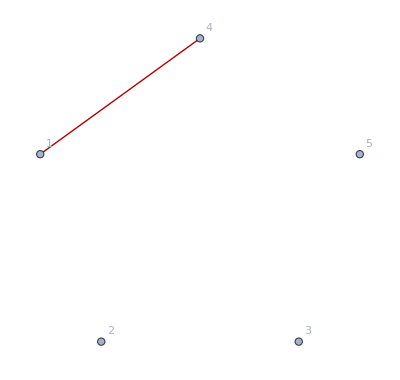
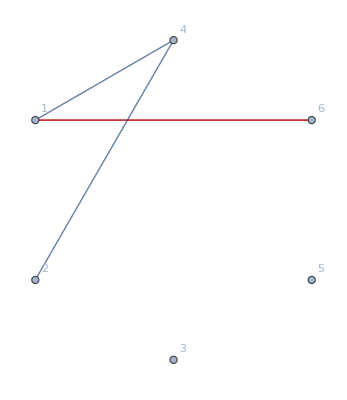
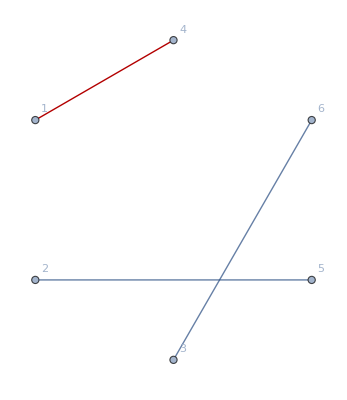
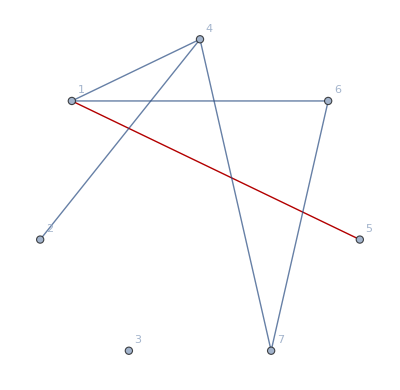
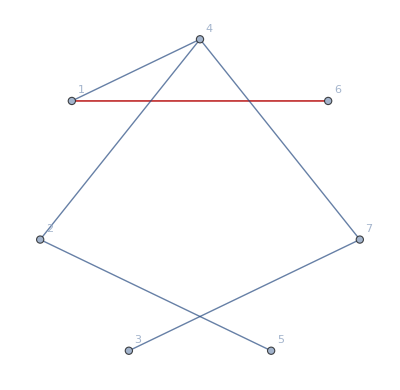
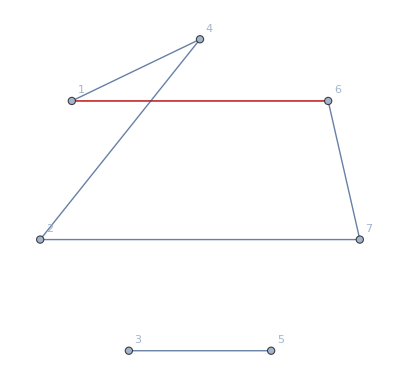
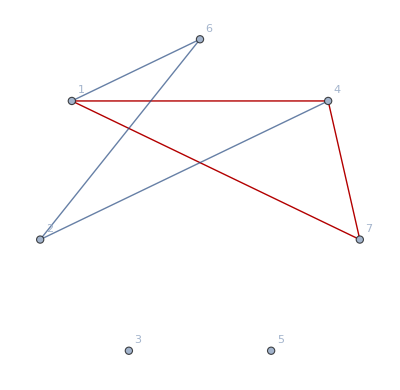
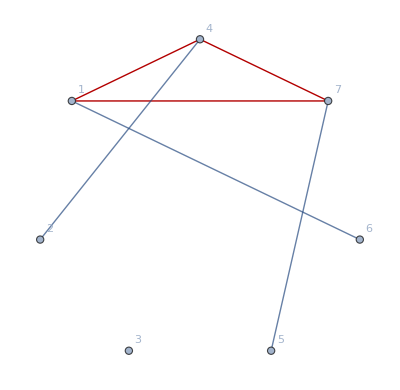
{n
5
remove
1→{-Graphics-},n
6
remove
3→{-Graphics-,-Graphics-},n
7
remove
6→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},n
8
remove
10→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},n
9
remove
15→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[Column[{"n",Style[count,Red],"remove",(count-3)(count-4)/2}]->Map[
With[{g=GraphComplement[First[#],GraphLayout->"CircularEmbedding"]},
Graph[VertexList[g],EdgeList[g],GraphHighlight->Map[#[[1]]<->#[[2]]&,Flatten[Table[Subsets[s,{2}],{s,FindClique[g]}],1]],GraphHighlightStyle->"Thick",GraphLayout->"CircularEmbedding",VertexLabels->"Name"]
]
&,Tally[Select[grofs,VertexCount[#]==count&],IsomorphicGraphQ]
],{count,5,9}]
```